The difference between the “lite_network” and “baby_network” is that in the “lite” one I commented out info for URL, hash, citation, type, includesAlg, and verified (basically, all the longer strings except the title, and verified as well since it’s not necessary). Maybe also type and includesAlg? Since they’ll only exist for very few of them. Since it makes it take waaaaaaaay longer. This way we should be able to see if the floats make it worse.

```mathematica
AppendTo[$Path, FileNameJoin[{$HomeDirectory,"network-similarity"}]];
```

```mathematica
g = Import["citation_network.gml"];
```

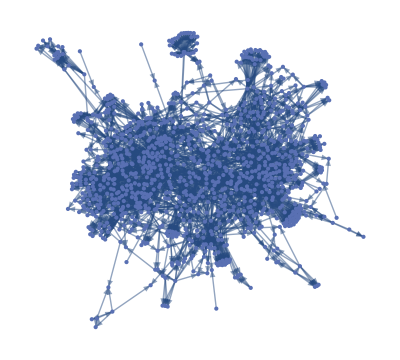

```mathematica
outdegrees = VertexOutDegree[g];
indegrees = VertexInDegree[g];
parents = Position[outdegrees, _?(#>0&)] // Flatten;popular = Position[indegrees, _?(#>1&)] // Flatten;
g1= Subgraph[g, Union[parents, popular],Options[g], VertexSize->Large];
gCC =Subgraph[g1,WeaklyConnectedComponents[g1][[1]],Options[g1], ImageSize->Full]
```

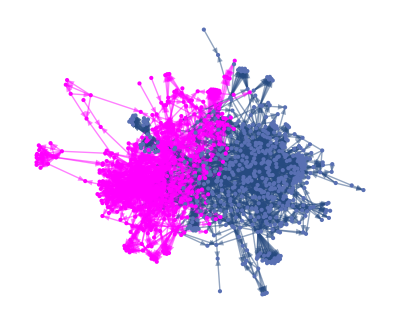

```mathematica
partition = FindGraphPartition[gCC,2];
gA = Subgraph[gCC, partition[[1]], Options[gCC]];
gB = Subgraph[gCC, partition[[2]], Options[gCC]];
HighlightGraph[gCC,Style[gA,RGBColor["Fuchsia"]],GraphHighlightStyle->"Thick",ImageSize->Full]
```

```mathematica
file1= FileNameJoin[{$HomeDirectory,"network-similarity\\top_gCC.txt"}];
Close[file1];OpenWrite[file1];Close[file1];
file1 = OpenAppend[file1];
fileA= FileNameJoin[{$HomeDirectory,"network-similarity\\top_gA.txt"}];
Close[fileA];OpenWrite[fileA];Close[fileA];
fileA = OpenAppend[fileA];
fileB = FileNameJoin[{$HomeDirectory, "network-similarity\\top_gB.txt"}];
Close[fileB];OpenWrite[fileB];Close[fileB];
fileB = OpenAppend[fileB];
```

```mathematica
WriteString[file1, ">>> Indegree <<<\n"];
WriteString[fileA, ">>> Indegree <<<\n"];
WriteString[fileB, ">>> Indegree <<<\n"];
tops = Part[VertexList[gCC], Ordering[DegreeCentrality[gCC,"In"], All, Greater]];
For[i=1,i≤10,i++,
WriteString[file1,"Node ", tops[[i]], ", indegree ", VertexInDegree[gCC, tops[[i]]], ", '", PropertyValue[{gCC,tops[[i]]},"title"], "'\n"]]
tops = Part[VertexList[gA], Ordering[DegreeCentrality[gA,"In"], All, Greater]];
For[i=1,i≤10,i++,
WriteString[fileA,"Node ", tops[[i]], ", indegree ", VertexInDegree[gA, tops[[i]]], ", '", PropertyValue[{gA,tops[[i]]},"title"], "'\n"]]
tops = Part[VertexList[gB], Ordering[DegreeCentrality[gB,"In"], All, Greater]];
For[i=1,i≤10,i++,
WriteString[fileB,"Node ", tops[[i]], ", indegree ", VertexInDegree[gB, tops[[i]]], ", '", PropertyValue[{gB,tops[[i]]},"title"], "'\n"]]
```

```mathematica
WriteString[fileA, ">>> Outdegree <<<\n"];
WriteString[fileB, ">>> Outdegree <<<\n"];
tops = Part[VertexList[gA], Ordering[DegreeCentrality[gA,"Out"], All, Greater]];
For[i=1,i≤10,i++,
WriteString[fileA,"Node ", tops[[i]], ", outdegree ", VertexOutDegree[gA, tops[[i]]], ", '", PropertyValue[{gA,tops[[i]]},"title"], "'\n"]]
tops = Part[VertexList[gB], Ordering[DegreeCentrality[gB,"In"], All, Greater]];
For[i=1,i≤10,i++,
WriteString[fileB,"Node ", tops[[i]], ", outdegree ", VertexOutDegree[gB, tops[[i]]], ", '", PropertyValue[{gB,tops[[i]]},"title"], "'\n"]]
```

```mathematica
WriteString[fileA, ">>> Betweenness <<<\n"];
WriteString[fileB, ">>> Betweenness <<<\n"];
tops = Part[VertexList[gA], Ordering[BetweennessCentrality[gA], All, Greater]];
For[i=1,i≤10,i++,
WriteString[fileA,"Node ",tops[[i]], ", '",PropertyValue[{gA,tops[[i]]},"title"], "'\n"]]
tops = Part[VertexList[gB], Ordering[BetweennessCentrality[gB], All, Greater]];
For[i=1,i≤10,i++,
WriteString[fileB,"Node ",tops[[i]], ", '",PropertyValue[{gB,tops[[i]]},"title"], "'\n"]]
```

```mathematica
WriteString[fileA, ">>> PageRank <<<\n"];
WriteString[fileB, ">>> PageRank <<<\n"];
tops = Part[VertexList[gA], Ordering[PageRankCentrality[gA], All, Greater]];
For[i=1,i≤10,i++,
WriteString[fileA,"Node ",tops[[i]], ", '",PropertyValue[{gA,tops[[i]]},"title"], "'\n"]]
tops = Part[VertexList[gB], Ordering[PageRankCentrality[gB], All, Greater]];
For[i=1,i≤10,i++,
WriteString[fileB,"Node ",tops[[i]], ", '",PropertyValue[{gB,tops[[i]]},"title"], "'\n"]]
```

```mathematica
WriteString[fileA, ">>> Closeness <<<\n"];
WriteString[fileB, ">>> Closeness <<<\n"];
tops = Part[VertexList[gA], Ordering[ClosenessCentrality[gA], All, Greater]];
For[i=1,i≤10,i++,
WriteString[fileA,"Node ",tops[[i]], ", '",PropertyValue[{gA,tops[[i]]},"title"], "'\n"]]
tops = Part[VertexList[gB], Ordering[ClosenessCentrality[gB], All, Greater]];
For[i=1,i≤10,i++,
WriteString[fileB,"Node ",tops[[i]], ", '",PropertyValue[{gB,tops[[i]]},"title"], "'\n"]]
```